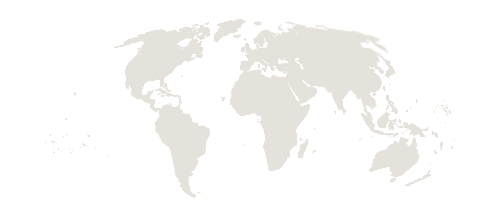

```mathematica
CountryData["World",{"Shape","Mollweide"}]
```

```mathematica
CountryData["Australia","SchematicPolygon"]
```

Polygon[{{{144.633,-38.3333},{143.55,-38.8667},{140.367,-37.95},{139.483,-35.9167},{138.083,-34.15},{136.833,-35.3},{137.767,-32.5167},{135.95,-34.9833},{133.783,-32.2167},{131.2,-31.4833},{125.983,-32.3167},{120.017,-33.9333},{117.95,-35.15},{115.117,-34.3833},{115.733,-31.9},{113.15,-26.15},{114.233,-26.1333},{113.4,-24.1667},{114.033,-21.8167},{116.817,-20.5},{121.033,-19.5333},{122.933,-16.3667},{123.767,-17.8833},{123.617,-16.1333},{125.25,-15.5833},{126.017,-13.9},{127.417,-13.95},{127.833,-15.6},{128.483,-14.7667},{130.2,-15.3833},{129.7,-13.8833},{131.,-12.1667},{132.683,-12.1833},{131.983,-11.2},{135.717,-12.3},{136.983,-12.4},{135.45,-14.9833},{140.1,-17.7167},{141.717,-15.2333},{142.133,-11.0333},{143.1,-12.2},{143.783,-14.3833},{145.367,-14.9667},{146.283,-18.8833},{148.783,-20.25},{149.633,-22.55},{150.8,-22.5333},{152.917,-25.3},{153.617,-28.7833},{150.217,-35.7333},{149.617,-37.7167},{146.367,-39.15},{144.633,-38.3333}},{{153.033,-25.7667},{153.267,-24.7},{153.033,-25.7667}},{{145.767,-43.1667},{144.7,-40.6833},{148.35,-40.9667},{147.983,-43.1833},{145.767,-43.15}},{{130.933,-11.9333},{130.383,-11.2},{131.433,-11.3},{130.933,-11.9333}}}]

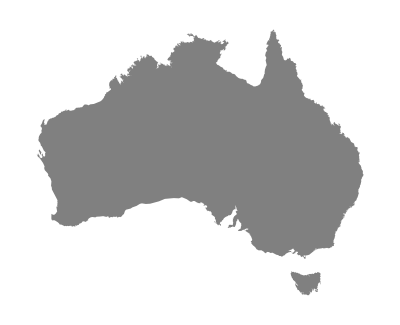

```mathematica
Graphics[{Gray,CountryData["Australia","Polygon"]}]
```

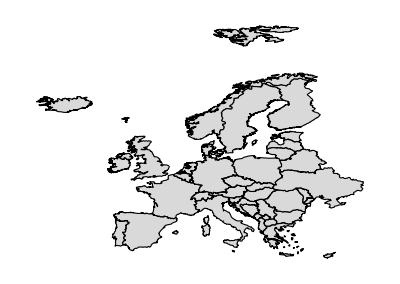

```mathematica
Graphics[{EdgeForm[Black],LightGray,CountryData[#,"Polygon"]&/@CountryData["Europe"]}]
```

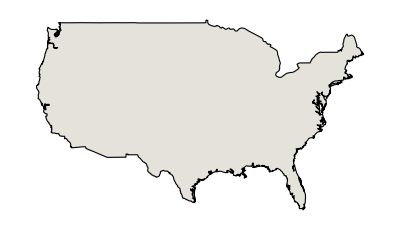

```mathematica
CountryData["UnitedStates",{"Shape",{"Mollweide",Center}}]
```

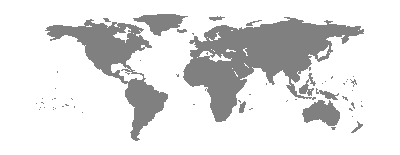

```mathematica
Graphics[{Gray,CountryData[#,"SchematicPolygon"]&/@CountryData[]}]
```

```mathematica
CountryData["cz",{"Shape"}]
```

CountryData::notent: "\"cz\"" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

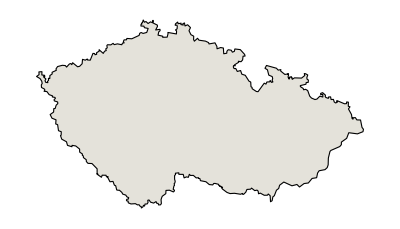

```mathematica
CountryData["CzechRepublic","Shape"]
```

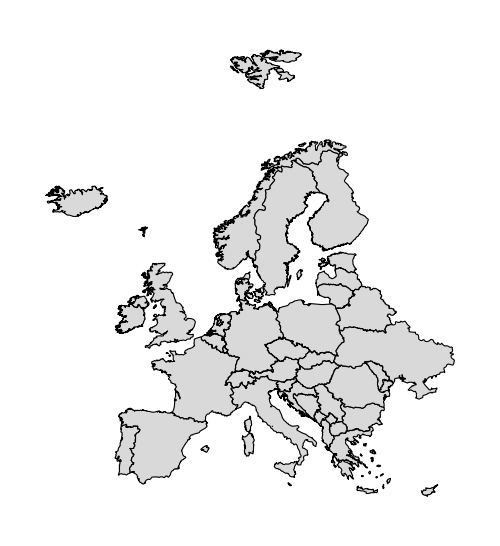

```mathematica
Graphics[{EdgeForm[Black],LightGray,CountryData[#,{"Polygon", "WinkelTripel"}]&/@CountryData["Europe"]}]
```

```mathematica
CountryData[#,{"SchematicPolygon", "WinkelTripel"}]&/@CountryData["Europe"]
```

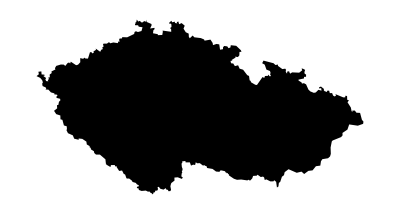

```mathematica
Graphics[CountryData["CzechRepublic",{"Polygon", "WinkelTripel"}]]
```

```mathematica
file
```

```mathematica
Export["czech_polygon.txt",CountryData["CzechRepublic",{"Polygon", "WinkelTripel"}], "Table"]
```

czech_polygon.txt

```mathematica
Directory[]
```

C:\Users\bzamecnik\Documents

```mathematica
czechrep = CountryData["CzechRepublic",{"Polygon", "WinkelTripel"}];
```

```mathematica
Export["europe.txt",CountryData[#,{"Polygon","WinkelTripel"}]&/@CountryData["Europe"]]
```

europe.txt